## Kernels

```mathematica
Needs["SubKernels`RemoteKernels`"]
```

```mathematica
LaunchKernels[RemoteMachine["server",7]]
```

```mathematica
LaunchKernels[RemoteMachine["node01",8]]
```

```mathematica
LaunchKernels[RemoteMachine["node02",8]]
```

```mathematica
LaunchKernels[RemoteMachine["node03",8]]
```

```mathematica
LaunchKernels[RemoteMachine["node04",8]]
```

## Init

```mathematica
(*rotation*)
R={{1/Sqrt[2],0,0,0,0,1/Sqrt[2],0,0},{0,1/Sqrt[2],0,0,0,0,1/Sqrt[2],0},{0,0,1/2,0,0,0,0,Sqrt[3]/2},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{-1/Sqrt[2],0,0,0,0,1/Sqrt[2],0,0},{0,-1/Sqrt[2],0,0,0,0,1/Sqrt[2],0},{0,0,-Sqrt[3]/2,0,0,0,0,1/2}};
```

```mathematica
(*Definition of the f-tensor*)
f[i_,j_,k_]:=0;

f[1,2,3]=f[2,3,1]=f[3,1,2]=1;
 
f[1,3,2]=f[2,1,3]=f[3,2,1]=-1;

f[1,4,7]= f[4,7,1]=f[7,1,4]=
f[1,6,5]=f[6,5,1]=f[5,1,6]=
 f[2,4,6]= f[4,6,2]= f[6,2,4]=
f[2,5,7]=f[5,7,2]=f[7,2,5]=
 f[3,4,5]= f[4,5,3]= f[5,3,4]=
 f[3,7,6]=  f[7,6,3]= f[6,3,7]=1/2;

f[1,7,4]=f[7,4,1]=f[4,1,7]=
f[1,5,6]=f[5,6,1]=f[6,1,5]=
 f[2,6,4]= f[6,4,2]= f[4,2,6]=
f[2,7,5]=f[7,5,2]=f[5,2,7]=
 f[3,5,4]= f[5,4,3]= f[4,3,5]=
 f[3,6,7]= f[6,7,3]= f[7,3,6]=-1/2;
```

```mathematica
f[4,5,8]=f[5,8,4]=f[8,4,5]=
 f[6,7,8]= f[7,8,6]= f[8,6,7]=Sqrt[3]/2; 

f[4,8,5]=f[8,5,4]=f[5,4,8]=
 f[6,8,7]= f[8,7,6]= f[7,6,8]=-Sqrt[3]/2; 

(*Definition of the d-tensor*)

d[i_,j_,k_]=0;
d[1,1,8]=d[1,8,1]=d[8,1,1]=
d[2,2,8]=d[2,8,2]=d[8,2,2]=
d[3,3,8]=d[3,8,3]=d[8,3,3]=1/Sqrt[3];
d[8,8,8]=-(1/Sqrt[3]);
d[1,4,6]=d[1,6,4]=d[4,1,6]=d[4,6,1]=d[6,1,4]=d[6,4,1]=
d[1,5,7]=d[1,7,5]=d[5,1,7]=d[5,7,1]=d[7,1,5]=d[7,5,1]=
d[2,5,6]=d[2,6,5]=d[5,2,6]=d[5,6,2]=d[6,2,5]=d[6,5,2]=
d[3,4,4]=d[4,3,4]=d[4,4,3]=
d[3,5,5]=d[5,3,5]=d[5,5,3]=1/2;
d[2,4,7]=d[2,7,4]=d[4,2,7]=d[4,7,2]=d[7,2,4]=d[7,4,2]=
d[3,6,6]=d[6,3,6]=d[6,6,3]=
d[3,7,7]=d[7,3,7]=d[7,7,3]=-(1/2);
d[4,4,8]=d[4,8,4]=d[8,4,4]=
d[5,5,8]=d[5,8,5]=d[8,5,5]=
d[6,6,8]=d[6,8,6]=d[8,6,6]=
d[7,7,8]=d[7,8,7]=d[8,7,7]=-(1/(2Sqrt[3]));
```

## Constants

```mathematica
Get["constants.m"]
```

## Dynamic Equations

```mathematica
vν=Table[Table[ν[m,n][t],{n,1,8}],{m,1,Sites}];
vνcor=Table[Table[ν[m,n][t]ν[l,n][t],{n,1,8}],{m,1,Sites},{l,1,Sites}];
dν=Table[Table[ν[m,n]'[t],{n,1,8}],{m,1,Sites}];
initialsν=Flatten[Table[Table[ν[m,n][0]==Subscript[ν, 0][m,n],{n,1,8}],{m,1,Sites}]];
Δν[m_,ow_]:=Table[D[ow,ν[m,n][t]],{n,1,8}];
```

```mathematica
vq=Table[vν[[m]].R,{m,1,Sites}];
dq=Table[dν[[m]].R,{m,1,Sites}];
Δq[m_,ow_]:=Δν[m,ow].R;
```

```mathematica
νw[m_,ow_]:=vν[[m]] ow+I/2 Table[Sum[R[[n,a]]f[a,b,c]vq[[m,c]]Δq[m,ow][[b]],{b,1,8},{c,1,8},{a,1,8}],{n,1,8}];
νwb[m_,ow_]:=vν[[m]] ow-I/2 Table[Sum[R[[n,a]]f[a,b,c]vq[[m,c]]Δq[m,ow][[b]],{b,1,8},{c,1,8},{a,1,8}],{n,1,8}];
```

```mathematica
sxν[m_,ow_]:= 2νw[m,ow][[1]];
syν[m_,ow_]:= 2νw[m,ow][[2]];
szν[m_,ow_]:= 2νw[m,ow][[3]];
szsν[m_,ow_]:=2(-1/Sqrt[3])νw[m,ow][[8]];
sxνb[m_,ow_]:= 2νwb[m,ow][[1]];
syνb[m_,ow_]:= 2νwb[m,ow][[2]];
szνb[m_,ow_]:= 2νwb[m,ow][[3]];
szsνb[m_,ow_]:=2(-1/Sqrt[3])νwb[m,ow][[8]];
```

```mathematica
(*Hν[m_,ow_]:=U/2szsν[m,ow]-Jx  sxν[m,ow](Sum[sxν[n,1],{n,1,m-1}]+Sum[sxν[n,1],{n,m+1,Sites}])-Jy syν[m,ow](Sum[syν[n,1],{n,1,m-1}]+Sum[syν[n,1],{n,m+1,Sites}])-μ szν[m,ow];
Hνb[m_,ow_]:=U/2szsνb[m,ow]-Jx sxνb[m,ow](Sum[sxνb[n,1],{n,1,m-1}]+Sum[sxνb[n,1],{n,m+1,Sites}])-Jy syνb[m,ow](Sum[syνb[n,1],{n,1,m-1}]+Sum[syνb[n,1],{n,m+1,Sites}])-μ szνb[m,ow];*)
```

```mathematica
(*eqnsν1=Table[dν[[1,n]]==Simplify[ⅈ (Hν[1,vν[[1,n]]]-Hνb[1,vν[[1,n]]])],{n,1,8}]*)
```

```mathematica
eqnsν1={Derivative[1][ν[1,1]][t]==μ ν[1,2][t]+1/2 U ν[1,7][t]-2 Jy ν[1,3][t] ν[2,2][t],Derivative[1][ν[1,2]][t]==-μ ν[1,1][t]-1/2 U ν[1,6][t]+2 Jx ν[1,3][t] ν[2,1][t],Derivative[1][ν[1,3]][t]==-2 Jx ν[1,2][t] ν[2,1][t]+2 Jy ν[1,1][t] ν[2,2][t],Derivative[1][ν[1,4]][t]==2 (μ ν[1,5][t]+Jx ν[1,7][t] ν[2,1][t]+Jy ν[1,6][t] ν[2,2][t]),Derivative[1][ν[1,5]][t]==-2 (μ ν[1,4][t]+Jx ν[1,6][t] ν[2,1][t]-Jy ν[1,7][t] ν[2,2][t]),Derivative[1][ν[1,6]][t]==1/2 U ν[1,2][t]+μ ν[1,7][t]+2 Jx ν[1,5][t] ν[2,1][t]-2 Jy ν[1,4][t] ν[2,2][t]-2 Sqrt[3] Jy ν[1,8][t] ν[2,2][t],Derivative[1][ν[1,7]][t]==-(1/2) U ν[1,1][t]-μ ν[1,6][t]-2 Jx ν[1,4][t] ν[2,1][t]+2 Sqrt[3] Jx ν[1,8][t] ν[2,1][t]-2 Jy ν[1,5][t] ν[2,2][t],Derivative[1][ν[1,8]][t]==2 Sqrt[3] (-Jx ν[1,7][t] ν[2,1][t]+Jy ν[1,6][t] ν[2,2][t])};
```

```mathematica
eqnsν=Flatten[Table[eqnsν1/.Flatten[Table[{ν[1,n]'[t]->ν[m,n]'[t],ν[1,n][t]->ν[m,n][t],ν[2,n][t]->(Sum[ν[l,n][t],{l,1,m-1}]+Sum[ν[l,n][t],{l,m+1,Sites}])},{n,1,8}]],{m,1,Sites}]];
```

```mathematica
(*MatrixForm[eqnsν]*)
```

## SU3 Wigner with neg prob

```mathematica
νvarsingreek={((α+γ) Conjugate[β]+β (Conjugate[α]+Conjugate[γ]))/(2 Sqrt[2]),-((I (β Conjugate[α]+(-α+γ) Conjugate[β]-β Conjugate[γ]))/(2 Sqrt[2])),1/2 (Abs[α]^2-γ Conjugate[γ]),1/2 (γ Conjugate[α]+α Conjugate[γ]),-(1/2) I (γ Conjugate[α]-α Conjugate[γ]),(-β Conjugate[α]+(-α+γ) Conjugate[β]+β Conjugate[γ])/(2 Sqrt[2]),(I (-(α+γ) Conjugate[β]+β (Conjugate[α]+Conjugate[γ])))/(2 Sqrt[2]),-((Abs[α]^2+Abs[γ]^2-2 β Conjugate[β])/(2 Sqrt[3]))};
```

```mathematica
Norm1=(4-Sqrt[E])/Sqrt[E];
```

```mathematica
Fock1Mag=ProbabilityDistribution[4 a E^(-2 a^2) Abs[(4a^2-1)]/Norm1,{a,0,∞}];
```

```mathematica
Dynamic[su3Runsdone]
```

```mathematica
spindyn=Table[0,{Nt},{1},{2}];
SetSharedVariable[spindyn];
spincordyn=Table[0,{Nt},{1},{4}];
SetSharedVariable[spincordyn];
su3Runsdone=0;
SetSharedVariable[su3Runsdone];
Timing[
ParallelDo[
randupinit[n_]:={randmag[[n]] E^(I randphase[[n]]),randrest[[1,n]],randrest[[2,n]]};
randmiinit[n_]:={randrest[[1,n]],randmag[[n]] E^(I randphase[[n]]),randrest[[2,n]]};
randdoinit[n_]:={randrest[[1,n]],randrest[[2,n]],randmag[[n]] E^(I randphase[[n]])};
randmag=RandomVariate[Fock1Mag,{Sites}];
metric=1-2UnitStep[1/2-randmag];
randphase=RandomReal[{0,2π},{Sites}];
randrest=Table[RandomVariate[NormalDistribution[0,1/2]]+I RandomVariate[NormalDistribution[0,1/2]],{2},{su3Runs}];
randinits=Table[randupinit[n],{n,1,updownmiddle[[1]]}]~Join~Table[randdoinit[n],{n,updownmiddle[[1]]+1,updownmiddle[[1]]+updownmiddle[[2]]}]~Join~Table[randmiinit[n],{n,updownmiddle[[1]]+updownmiddle[[2]]+1,updownmiddle[[1]]+updownmiddle[[2]]+updownmiddle[[3]]}];
sol=NDSolve[(eqnsν~Join~initialsν)/.{U->Uvalue,μ->μvalue,J->Jvalue,navg->navgvalue}~Join~Flatten[Table[Subscript[ν, 0][m,n]->(νvarsingreek[[n]]/.{α->randinits[[m,1]],β->randinits[[m,2]],γ->randinits[[m,3]]}),{m,1,Sites},{n,1,8}]],Flatten[vν],{t,0,tmax},MaxSteps->∞
];
metprod=Product[metric[[n]],{n,1,Sites}];
TWAresspin=metprod {ν[1,3][t],ν[2,3][t]}/.sol;
TWArescor=metprod{ν[1,8][t],ν[2,8][t],ν[1,8][t]ν[1,8][t],ν[2,8][t]ν[2,8][t]}/.sol;
spindyn+=Table[TWAresspin,{t,ts}];
spincordyn+=Table[TWArescor,{t,ts}];
su3Runsdone++;
,{j,1,su3Runs}
]
]
avgspins3=Norm1^Sites Re[spindyn[[All,1]]]/su3Runs;
avgcor3=Norm1^Sites Re[spincordyn[[All,1]]]/su3Runs;
```

$Aborted

```mathematica
{5.67996899999999982355802785605192184448`6.774945878714996,Null}
```

```mathematica
Save[su3outfile<>"spn.lst",avgspins3]
Save[su3outfile<>"corn.lst",avgcor3]
```

```mathematica
ListPlot[{times,avgspins3[[All,1]]}ᵀ]
```

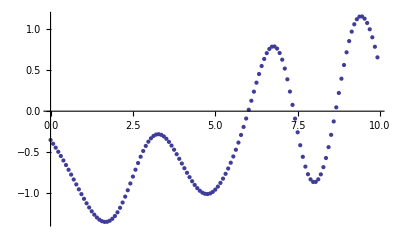

```mathematica
ListPlot[{times,avgcor3[[All,2]]}ᵀ]
```

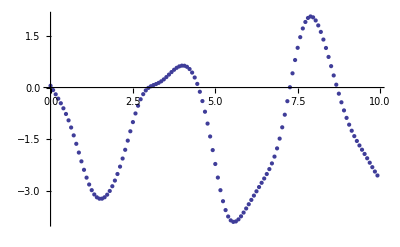

```mathematica
ListPlot[{times,avgcor3[[All,4]]}ᵀ]
```